```mathematica
SetDirectory[NotebookDirectory[]];
CvData = Import["32_cv.dat","Table"];
MagnetData = Import["32_magnetization.dat","Table"];
SusceptData = Import["32_susceptibility.dat","Table"];
```

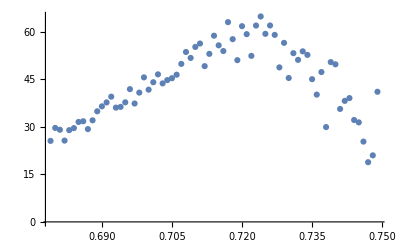

```mathematica
ListPlot[Take[SusceptData,{380, 450}], PlotRange->Full]
```

```mathematica
SusceptFit = NonlinearModelFit[Take[SusceptData,{380,450}],A*Exp[-( x-mu)^2/(2 Sigma^2)],{{A,55},Sigma,mu},x];
```

```mathematica
SusceptFit[{"BestFit","ParameterTable"}]
```

{56.5891 ⅇ^(-652.212 (-0.717671+x)^2), | Estimate | Standard Error | t-Statistic | P-Value
A | 56.5891 | 1.02718 | 55.0919 | 3.74056×10^-58
Sigma | -0.0276879 | 0.000965087 | -28.6896 | 1.02039×10^-39
mu | 0.717671 | 0.000657431 | 1091.63 | 5.00514×10^-146}

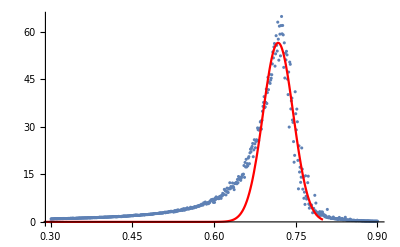

```mathematica
Show[ListPlot[SusceptData, PlotRange->Full],Plot[SusceptFit[x],{x,0,0.8},PlotRange->{{0,0.8},{0,500}}, PlotStyle->Red]]
```

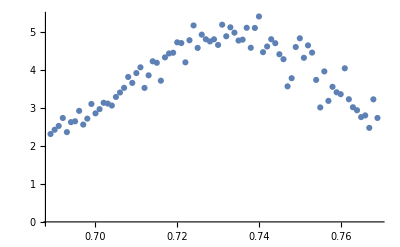

```mathematica
ListPlot[Take[CvData,{390,470}]]
```

```mathematica
CvFit = NonlinearModelFit[Take[CvData,{390,470}],A*Exp[-( x-mu)^2/(2*Sigma^2)],{{A,3.6},Sigma,mu},x]
```

FittedModel[4.86635 ⅇ^(-453.547 (-«19»+x)^2)]

```mathematica
CvFit[{"BestFit","ParameterTable"}]
```

{4.86635 ⅇ^(-453.547 (-0.732453+x)^2), | Estimate | Standard Error | t-Statistic | P-Value
A | 4.86635 | 0.0557354 | 87.3116 | 1.48697×10^-79
Sigma | -0.0332027 | 0.000777911 | -42.6819 | 7.69035×10^-56
mu | 0.732453 | 0.000503722 | 1454.08 | 1.15791×10^-174}

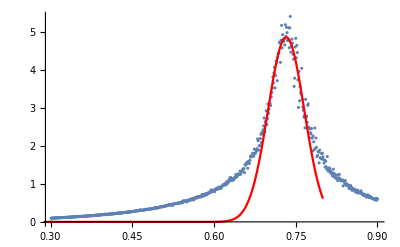

```mathematica
Show[ListPlot[CvData],Plot[CvFit[x],{x,0,0.8},PlotRange->Full,PlotStyle->Red]]
```